15000

3.2248

0.249986

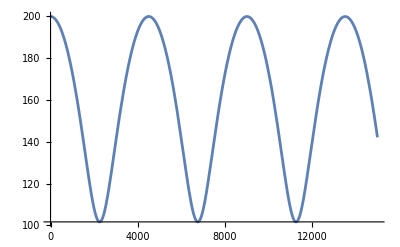

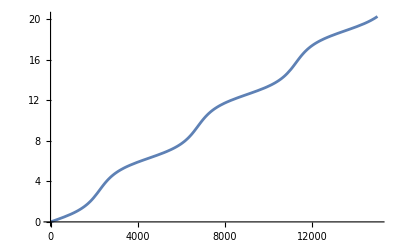

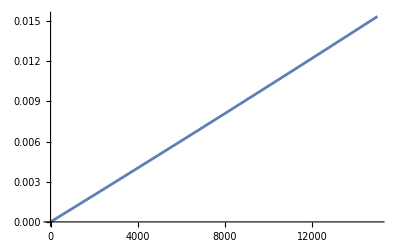

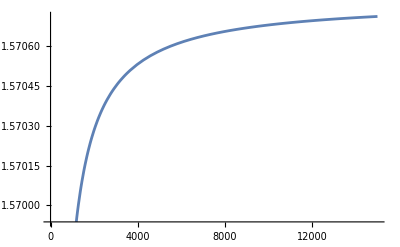

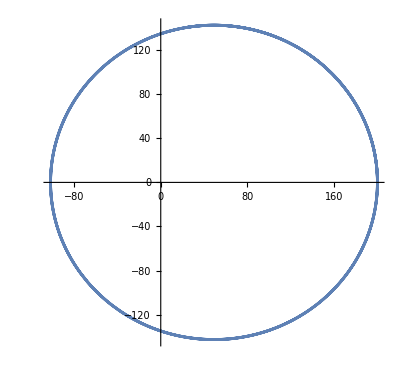

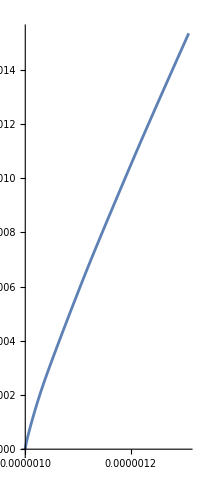

```mathematica
(*dichiaro tutte le variabili necessarie*)
vi= 0.15;
ri=200;
vs = 0.000001;
rs= 0.000001;
vang=vi/ri;
vangs = vs/rs;
G=6.6743*10^-11;
mterra= 1000;
msole= 10*10^10;
T =15000
(*imposto il sistema differenziale*)
sol=Simplify[NDSolve[{mterra*(r''[t]-r[t]*(f'[t])^2)==-(G*(mterra*msole/(r[t]-R[t])^2)),mterra*(2*r'[t]*f'[t]+r[t]*f''[t])==0,msole*(R''[t]-R[t]*(F'[t])^2)==(G*(mterra*msole/(R[t]-r[t])^2)),mterra*(2*R'[t]*F'[t]+R[t]*F''[t])==0,r[0]==ri,r'[0]==0,f'[0]==vang,f[0]==0, R[0]==rs,R'[0]==0,F'[0]==vangs,F[0]==0},{r[t],f[t], R[t], F[t]},{t,0,T}]]//Flatten;

(*risolvo e mi occupo del graficare*)
rf[t_]=r[t]/. sol;
ff[t_]=f[t]/. sol;
RF[t_]=R[t]/. sol;
FF[t_]=F[t]/. sol;
ff[T]/(2*Pi)
FF[T]/(2*Pi)
Plot[rf[t],{t,0,T}]
Plot[ff[t],{t,0,T}]
Plot[RF[t],{t,0,T}]
Plot[FF[t],{t,0,T}]
ParametricPlot[{rf[t]*Cos[ff[t]],rf[t]*Sin[ff[t]]},{t,0,T}]
ParametricPlot[{RF[t]*Cos[FF[t]],RF[t]*Sin[FF[t]]},{t,0,T}]
```